## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
results={};
n=12;
primes=nprimes[n][[;;10000]];
```

## Prime 12

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks12 =naturalVisibility[series];
```

## Graph

```mathematica
igv12=Graph[natLinks12, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv12];
```

```mathematica
count = Total[adj]//Counts
```

<|3→1762,6→927,11→217,4→1695,8→475,20→53,2→1287,5→1248,13→120,14→114,10→289,17→63,18→45,28→18,7→681,16→62,9→332,19→43,25→27,37→3,12→173,27→18,44→3,15→101,31→7,59→2,36→5,32→8,21→37,46→1,58→2,121→1,35→5,29→9,30→9,24→19,22→38,23→25,26→18,34→9,52→1,40→4,39→11,41→4,38→2,62→2,54→1,50→2,45→1,33→5,49→4,55→1,42→2,60→2,98→1,89→1,47→1,53→1,51→1,1→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{3,1762/9999},{6,103/1111},{11,217/9999},{4,565/3333},{8,475/9999},{20,53/9999},{2,13/101},{5,416/3333},{13,40/3333},{14,38/3333},{10,289/9999},{17,7/1111},{18,5/1111},{28,2/1111},{7,227/3333},{16,62/9999},{9,332/9999},{19,43/9999},{25,3/1111},{37,1/3333},{12,173/9999},{27,2/1111},{44,1/3333},{15,1/99},{31,7/9999},{59,2/9999},{36,5/9999},{32,8/9999},{21,37/9999},{46,1/9999},{58,2/9999},{121,1/9999},{35,5/9999},{29,1/1111},{30,1/1111},{24,19/9999},{22,38/9999},{23,25/9999},{26,2/1111},{34,1/1111},{52,1/9999},{40,4/9999},{39,1/909},{41,4/9999},{38,2/9999},{62,2/9999},{54,1/9999},{50,2/9999},{45,1/9999},{33,5/9999},{49,4/9999},{55,1/9999},{42,2/9999},{60,2/9999},{98,1/9999},{89,1/9999},{47,1/9999},{53,1/9999},{51,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.418924/x^1.07833]

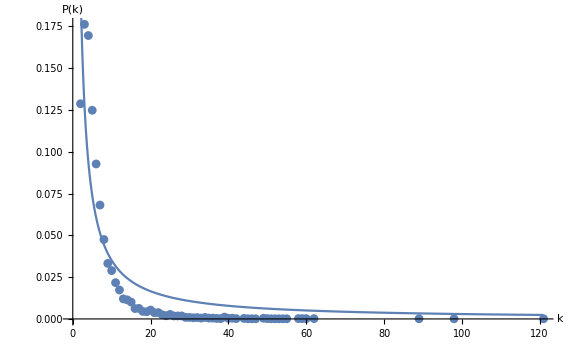

```mathematica
vis12=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igv12]//Mean//N
```

6.40264

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks12=horizontalVisibility[series];
```

## Graph

```mathematica
igh12=Graph[horLinks12, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh12];
```

```mathematica
count = Total[adj]//Counts
```

<|1→2,3→2174,7→404,4→1451,9→159,2→3717,5→961,6→571,10→108,11→75,8→260,13→35,14→21,12→37,16→6,15→8,17→5,24→1,19→3,18→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{3,2174/9999},{7,4/99},{4,1451/9999},{9,53/3333},{2,413/1111},{5,961/9999},{6,571/9999},{10,12/1111},{11,25/3333},{8,260/9999},{13,35/9999},{14,7/3333},{12,37/9999},{16,2/3333},{15,8/9999},{17,5/9999},{24,1/9999},{19,1/3333},{18,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.25709/x^1.70076]

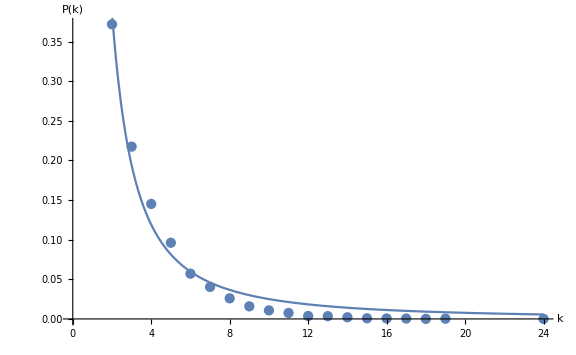

```mathematica
hvis12=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis12];
```

## Mean degree

```mathematica
degree=VertexDegree[igh12]//Mean//N
```

3.78338

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{horizontal,12,9999,3.78338,1.70076 ± 0.174654,1.25709 ± 0.213727},{visibility,12,9999,6.40264,1.07833 ± 0.178953,0.418924 ± 0.109128}}